### Mathematica Hw 3

Claus Ernst/Uta Ziegler		Department of Mathematics		Math/Cs 371 Spring 2019
Due: Wednesday, February 13 before class.

Form groups of two. However if at this point you had twice the same partner, you need to find a new partner. 
Each member of the group must understand and be able to explain (in detail) all of the code turned in. We allow you to work in groups so that you have someone with whom you can talk about your work in detail. This is not meant for group members to only do half of the work.

#### Submission details

The electronic submission will be made via Blackboard - using the submission link in the HW3 folder.

Turn in the following (hard copy prior to class):
1)  A completed evaluation form.

Turn in the following electronically (prior to class; see the two videos in the HW1 folder for the submission and the mandatory testing):
Turn in one .zip file which is the result of zipping up a folder . The name of the folder (and of the zipfile)  must include the last names of all team members, e.g. ErnstZiegler371HW3. The folder must include the following two files: 
1) One file with solutions for the problems  
 
a) Include the problems, your solutions, and a couple of executions of your code which demonstrate that the code is (most likely) correct. Select different types of input for your example runs, to show that different parts of your code work correctly.  
b) Make sure that each function definition is in its own cell and set the cells with the function definitions (only those!) to "Initialization cell". 
c) The names of both group members must be included in the file. Additionally, the name of both group members must be part of the name of the electronic file. For example if we (Claus and Uta) are a team then the file name should be ErnstZiegler371Hw3.nb. This will help to identify whose file we are looking at and it will also avoid having several different files with the same name.

2) The mandatory testing file with the results computed by the functions you turned in as part of 1) (see videos in HW1 and HW2 folders)
a) Make sure that you include the name(s) of all team members into the file. 
b) Change the name of the file to include the last names of all team members (e.g. ErnstZiegler371HW3Testing.nb)

#### Problem 1: Random walks

#### I. RandomWalk 2D

Given an interval=[lower,upper] where 0≤lower<upper are integers.
Choose an integer start in interval.

a) Write a function randomWalk[lower, upper, start, steps] that creates and returns a list of steps+1 points with integer coordinates in the plane, that resemble a random walk. 
Starting at {0,start} we walk either one step up or one step down with equal probability (up or down affects the y-coordinate; the x-coordinate is increased by 1). That is our next point is with equal probability either  {1,start+1} or {1,start-1}. Now repeat the process steps-1 times - to get a total of steps steps (and steps+1 points). The walk my never leave the given interval. That means if the walk reaches upper (on the y-coordinate) the next step is forced to be a down step - there is no random decision here. If the walk reaches lower (on the y-coordinate), the next step is forced to be an up step - again without random decision. 
For example if lower =0 and upper = 10, start=7 and steps=4, then one possible output of randomWalk[lower, upper, start, steps] could be the list of pairs
{{0,7},{1,8},{2,9},{3,8},{4,9}}. 
However {{0,7},{1,8},{2,9},{3,10},{4,11}} is not a valid walk since 11 is not in the interval.

b) Write a function plotRandomWalk[lower, upper, start, steps] that creates a graphical output corresponding to the random walk generated in part a). plotRandomWalk must call randomWalk. The graphical output should look like shown below with the walk in blue and the points in red.

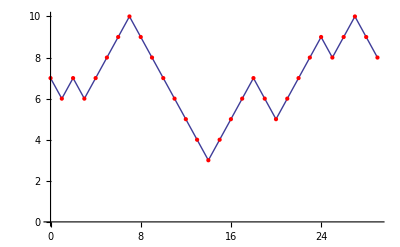

c) Write a function stopRandomWalk[lower, upper, start] that creates a random walk as in part a). However the length is not set, the function  simply stops the walk when the walk (more precisely: the y-coordinate) hits either the number upper or the number lower for the first time. stopRandomWalk[lower, upper, start] should returns the list of coordinates for the walk and a graph of the walk as well  (that is, it returns a list with two items: the plot and the list of points (in this order)). Modify this function to create a function stopPointRandomWalk[lower, upper, start]  that only returns the very last coordinate point of the walk, i.e. a single point with coordinates of the form {stop, lower} or {stop, upper} for some integer stop.

d) Write a function lowerUpper[lower, upper, start, repeat]  that uses the earlier function stopPointRandomWalk[lower, upper, start]. The function lowerUpper[lower, upper, start, repeat] runs stopPointRandomWalk[lower, upper, start] repeat many times and counts and returns how often the walk ends at lower and how often the walk ends at upper. The values are returned as a list with two elements - the first one being the number of times the walk ends at lower.
For example if repeat=10 the it might return {7,3} then this means in the 10 walks generated,  7 walks stopped when they reached the value lower (as y-coordinate) and 3 walks stopped when they reached the value upper (as y-coordinate).

#### II. Modified randomWalk 2D

Given an interval [lower,upper] where 0≤lower<upper are integers.
Choose an integer start in the interval.

a) Write a function modRandomWalk[lower, upper, start, probToStay, steps] that creates and returns a list of steps+1 points with integer coordinates in the plane, that resemble a random walk. 
Starting at {0,start} we either stay at the same y-coordinate with probability probToStay or walk one step up or one step down with equal probability (1-probToStay)/2 (up or down affects the y-coordinate; the x-coordinate is always increased by 1). That is next point is   {1,start},  {1,start+1} or {1,start-1}. Now repeat the process steps-1 times - to get a total of steps steps (and steps+1 points). The walk may never leave the given interval. That means if the walk reaches upper (on the y-coordinate) the next step is either down with probability (1-probToStay) or stay the same with probability probToStay. 
Similarly if the walk reaches lower.

b) Write a function modPlotRandomWalk[lower, upper, start, probToStay, steps] that creates a graphical output corresponding to the random walk generated in part a). modPlotRandomWalk must call modRandomWalk. The graphical output should look like shown below with the walk in blue and the points in red.

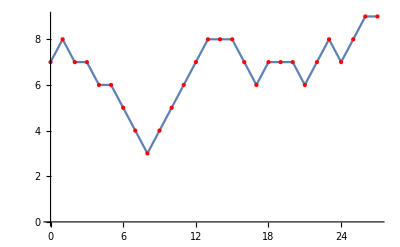

c) Write a function modStopRandomWalk[lower, upper,  probToStay, start] that creates a random walk as in part a). However the length is not set, the function  simply stops the walk when the walk (more precisely: the y-coordinate) hits either the number upper or the number lower for the first time. modStopRandomWalk[lower, upper,probToStay, start] should returns the list of coordinates for the walk and a graph of the walk as well  (that is, it returns a list with two items: the plot and the list of points (in that order)). Modify this function to create a function modStopPointRandomWalk[lower, upper, probToStay, start]  that only returns the very last coordinate point of the walk, i.e. a single point with coordinates of the form {stop, lower} or {stop, upper} for some integer stop.

#### III. RandomWalk 3D

Given a rectangle R in the y-z-plane defined by two pairs of coordinates {lower,upper} where lower and upper are pairs of integers that define the two opposite corners of a rectangle. For example if lower is {0,0} and upper is {10,20} then the rectangle is a five by ten rectangle with y-values 0≤y≤10 and with z-values 0≤z≤20. Choose an pair of integers {y_0,z_0} as start in the rectangle R.

a) Write a function randomWalk3D[lower, upper, start, steps] that creates and returns a list of steps+1 points with integer coordinates in 3-dimensional space, that resemble a random walk. Here lower and upper define the two opposite corners of a rectangle. 
Starting at {0,x_0,y_0} we walk either one step up or one step down with equal probability in the y-direction and at the same time one step up or one step down with equal probability in the z-direction and the x-coordinate is always increased by 1. That is our next point is with equal probability either  {1, y_0+1,z_0+1}, {1, y_0-1,z_0+1}, {1, y_0+1,z_0-1} or {1, y_0-1,z_0-1}. Now repeat the process steps-1 times - to get a total of steps steps (and steps+1 points). The y- and z-coordinates of the walk cannot leave the given rectangle. That means if the walk reaches upper (on the y- or z-coordinate) the next step is forced to be a down step in that coordinate - there is no random decision here. If the walk reaches lower (on the y- or z-coordinate), the next step is forced to be an up step in that coordinate - again without a random decision.  
For example if lower={0,0}, upper={10,15}, start={7,7} and steps=9, then one possible output of randomWalk3D[lower, upper, start, steps] could be the list of coordinates
{{0,7,7},{1,8,6},{2,7,5},{3,8,6},{4,7,5},{5,6,6},{6,5,5},{7,6,6},{8,5,7},{9,6,8}}

b) Write a function plotRandomWalk3D[lower, upper, start, steps] that creates a graphical output corresponding to the random walk generated in part a). plotRandomWalk3D must call randomWalk3D. The graphical output should look like shown below with the walk in blue and the points in red. The starting point should be shown in green.

```mathematica
plotRandomWalk3D[{0,0},{10,20},{ 7,7}, 40]
```

-Graphics3D-

c) Write a function stopRandomWalk3D[lower, upper, start] that creates a random walk as in part a). However the length is not set, the function  simply stops the walk when the walk (more precisely: the y- or z-coordinate) hits either the number in upper or the number in lower for the first time. stopRandomWalk3D[lower, upper, start] should returns the list of coordinates for the walk and a graph of the walk as well  (that is, it returns a list with two items: the plot and the list of points (in that order)). Modify this function to create a function stopPointRandomWalk3D[lower, upper, start]  that only returns the very last coordinate point of the walk, i.e. a single point with coordinates of the form {stop, lower_y lower_z} or {stop, upper_y, upper_z} for some integer stop.

```mathematica
stopRandomWalk3D[{0,0},{5,10},{ 2,7}]
```

{-Graphics3D-,{{0,2,7},{1,3,6},{2,2,5},{3,3,4},{4,2,5},{5,3,6},{6,2,7},{7,3,8},{8,2,7},{9,1,6},{10,0,7}}}

d) Write a function lowerUpper3D[lower, upper, start, repeat]  that uses the earlier function stopPointRandomWalk3D[lower, upper, start]. The function lowerUpper3D[lower, upper, start, repeat] runs stopPointRandomWalk3D[lower, upper, start] repeat many times and counts and returns how often the walk ends at lower y-coordinate, upper y -coordinate, lower z-coordinate  and upper z -coordinate. A fifth value indicates how many walks ended at a corner.
For example if repeat=10 the it might return {2,1,4,3, 0} then this means in the 10 walks generated,  2 walks stopped when they reached the value lower y-coordinate and 1 walk stopped when it reached the upper y-coordinate and so on. The 0 means none ended in a corner.  A second example if repeat = 10 a returned list of {2, 3, 4, 3, 2}, means that two of the walks ended in a corner and are counted twice. That is 2+3+4+3=12.

#### Problem 2: Wonderword

#### The general problem

Below is an example of a Wonderword game: A letterRect of letters and a list of words. The game consists of finding each of the words in the letterRect in any of the 8 directions. Any word appears exactly once. Letters which are not part of any of the words are the solution of the puzzle.  Note that a letter may be part of more than one word.
Here is the problem to be solved: Given a letterRect of letters and a list of words, check whether the letterRect makes up a Wonderword game. That means, check each word in the list to make sure it appears exactly most once. Your solution must return the following three pieces of information: 1) The list of words (from the given list of words) which were found exactly once; 2) The list of words which were found more than once. 3) The list of words which were not found at all. (The details of what to return are described below.)

Think about how you might approach this problem. Then follow the instructions below. Also, just like in the last homework, you should write several additional functions to simplify and modularize the work. Make sure you add good comments prior to each function which explains what its task is.

#### Representing the letterRect as a list of lists

The letterRect has rows and columns. Each row is a horizontal arrangement of letters. Rows are stacked vertically. The first row in the given example contains the letters “b”,”r”,”e”,”a”,”d”. The third row contains the letters “s”,”t”,”o”,”v”,”e”. A column is a vertical arrangement of letters. Columns are side-by-side. The first column in the given example contains the letters “b”, “m”, “s”, “f”, “g”.  Below is the code to specify a letterRect and how to display it nicely.

Note that the code specifies each row in a list, and the entire letterRect is a list of lists. Note that the first row is at the top of the letterRect and that moving from row to row+1 means moving down. Moving from  column to column +1 means moving to the right. The notation {row, col} is REVERSE from the usual {x,y} coordinates, but make it easy to access the letter in the letterRect. I recommend to stick with thinking about {row, col} to make it less likely that you switch the parameters.

```mathematica
letterRect={{"b","r","e","a","d"},{"m","o","u","s","e"},{"s","t","o","v","e"},{"f","l","o","w","r"},{"g","r","a","p","e"}};
display = Grid[letterRect, Frame->All]
```

b | r | e | a | d
m | o | u | s | e
s | t | o | v | e
f | l | o | w | r
g | r | a | p | e

Locations in the letterRect are specified by a pair: {row, col} and directions of moving from one letter to the next are also specified as a pair {changeInRow, changeInCol}. For example when starting in location {3, 2} and moving in direction {-1, 1}  leads to locations {3,2}, {2,3}, {1,4}, {0, 5}. The last one, of course, is not a valid location.

#### Functions needed to solve the problem

a) Write a function checkStartDirection [ letterRect, word, startLocation, direction] which is given a letterRect, a single word, a starting location, and a direction. The function returns true if the word is found when starting at the given location and moving in the given direction and false otherwise. The example call to checkStartDirection for the letterRect above. (You might first get the locations to be checked (see class code), then make sure that none are outside the letterRect, and then compare them to the needed letters.)

```mathematica
checkStartDirection[letterRect, "read", {1, 2},{0,1}]
```

True

```mathematica
checkStartDirection[letterRect, "read", {1, 3},{0,1}]
```

False

```mathematica
checkStartDirection[letterRect, "bead", {1, 3},{1,0}]
```

False

b) Write a function checkStart[letterRect, word, startLocation] which is given a letterRect, a single word, and a starting location. The function checks all possible directions for the given starting location. The function returns a list of the directions in which the word was found, or an empty list if the word was not found in any of the 8 possible directions.

```mathematica
checkStart[letterRect, "CPS",{4,5}]
```

{}

```mathematica
checkStart[letterRect, "re",{4,5}] (* note: was found in two direction *)
```

{{-1,0},{1,0}}

```mathematica
checkStart[letterRect, "pot",{5,4}]
```

{{-1,-1}}

c) Write a function findWord[letterRect, word] which is given a letterRect and a single word. The function checks all starting locations for the word. The function returns a list containing the results from checking all locations in the letterRect for the word. An empty list is returned if the word was not found at all. 

The result of the second example has two elements, that means there were two starting locations where it was found. The first element is {{1,2}, {{0,1}}}. The first element is the starting location and the second is the list of directions. So here there is only one direction: moving right. The second element is {{4,5}, {{-1, 0}, {1,0}}} which reports that from starting position {4,5} the word “re” was found twice one going down and one going to the left.

```mathematica
findWord[letterRect, "CPS"]
```

{}

```mathematica
findWord[letterRect, "re"]
```

{{{1,2},{{0,1}}},{{4,5},{{-1,0},{1,0}}}}

```mathematica
findWord[letterRect, "pot"]
```

{{{5,4},{{-1,-1}}}}

d) Write a function  findAllWords[letterRect, wordLst], which checks all the words in the wordLst and returns the matches. If a word was not found at all, no info about it is included in the result. For each word which has a multiple match return a list which indicates this: {“re”, “multiple matches”}. For words which have exactly one match return a list {word, matchinfo}, where matchinfo is the result of findWord.

```mathematica
wordlst={"kjhg","pan", "read", "top", "jhg","pot", "wolf", "deer", "sol", "rove", "reed","hg"};
```

```mathematica
wordlst2={"kjhg","pan", "read", "top","re", "jhg","pot", "wolf", "deer", "sol", "rove","to", "reed","hg"};
```

```mathematica
res =findAllWords[letterRect, wordlst]
```

{{read,{{{1,2},{{0,1}}}}},{top,{{{3,2},{{1,1}}}}},{pot,{{{5,4},{{-1,-1}}}}},{wolf,{{{4,4},{{0,-1}}}}},{deer,{{{1,5},{{1,0}}}}},{sol,{{{2,4},{{1,-1}}}}},{rove,{{{5,2},{{-1,1}}}}},{reed,{{{4,5},{{-1,0}}}}}}

```mathematica
res2=findAllWords[letterRect, wordlst2]
```

{{read,{{{1,2},{{0,1}}}}},{top,{{{3,2},{{1,1}}}}},{re,multiple matches},{pot,{{{5,4},{{-1,-1}}}}},{wolf,{{{4,4},{{0,-1}}}}},{deer,{{{1,5},{{1,0}}}}},{sol,{{{2,4},{{1,-1}}}}},{rove,{{{5,2},{{-1,1}}}}},{to,multiple matches},{reed,{{{4,5},{{-1,0}}}}}}

e) Write a function checkWonder[sq, wordlst] (which calls findAllWords) which returns a list containing three lists: a) the list of words from wordlst which appear exactly once b) the list of words from wordlst which appear more than once c) the list of words from wordlst which do not appear at all.

```mathematica
checkWonder[letterRect, wordlst]
```

{{read,top,pot,wolf,deer,sol,rove,reed},{},{hg,jhg,kjhg,pan}}

```mathematica
checkWonder[letterRect, wordlst2]
```

{{read,top,pot,wolf,deer,sol,rove,reed},{re,to},{hg,jhg,kjhg,pan}}

f) Bonus: Write a function checkWonder[sq, wordlst, color] (which calls findAllWords) which returns a list containing four items: a) the list of words from wordlst which appear exactly once b) the list of words from wordlst which appear more than once c) the list of words from wordlst which do not appear at all and d) the letterRect with the words found exactly once colored with the given color.

```mathematica
done =checkWonder[letterRect, wordlst]
```

{{read,top,pot,wolf,deer,sol,rove,reed},{},{hg,jhg,kjhg,pan}}

```mathematica
done =checkWonder[letterRect, wordlst, Purple]
```

{{read,top,pot,wolf,deer,sol,rove,reed},{},{deer,hg,jhg,kjhg,pan,pot,read,reed,rove,sol,top,wolf},{{b,r,e,a,d},{m,o,u,s,e},{s,t,o,v,e},{f,l,o,w,r},{g,r,a,p,e}}}

```mathematica
Grid[done[[4]],Frame->All]
```

b | r | e | a | d
m | o | u | s | e
s | t | o | v | e
f | l | o | w | r
g | r | a | p | e

```mathematica
done =checkWonder[letterRect, wordlst, {Blue, Orange}]
```

{{read,top,pot,wolf,deer,sol,rove,reed},{},{deer,hg,jhg,kjhg,pan,pot,read,reed,rove,sol,top,wolf},{{b,r,e,a,d},{m,o,u,s,e},{s,t,o,v,e},{f,l,o,w,r},{g,r,a,p,e}}}

```mathematica
Grid[done[[4]],Frame->All]
```

b | r | e | a | d
m | o | u | s | e
s | t | o | v | e
f | l | o | w | r
g | r | a | p | e

f) Bonus: Write a function checkWonder[sq, wordlst, color] (which calls findAllWords) which returns a list containing four items: a) the list of words from wordlst which appear exactly once b) the list of words from wordlst which appear more than once c) the list of words from wordlst which do not appear at all and d) the letterRect with the words found exactly once colored with the given color.